# Geographic Distortions

## George Varnavides, 01/29/2021

I’ve long been fascinated with transportation maps, and in particular the revolutionary re-design of the london-underground map by Harry Beck in 1933.

In his iconic design, which has since been adopted by most transportation maps, Harry Beck deliberately sacrifices geographic accuracy for visual clarity of information - by using equally-spaced stations on straight lines with only 45/90 degree bends

Here, we show how the local coordinate system is distorted through the years as more stations get added to display the information clearly

A note on the old transportation map figures:

I’ve had these on my machine from an old visual information project

I don’t believe these are publicly available on the web, so I’ll refrain from attaching these on the post

Contact me if you’re interested, and I can point you to where I got them from

References:

Beineke D. Verfahren zur Genauigkeitsanalyse fur Altkarten. Munchen: Universitat der Bundeswehr; 2001.

Jenny, Bernhard, and Lorenz Hurni. “Studying cartographic heritage: Analysis and visualization of geometric distortions.” Computers & Graphics 35.2 (2011): 402-411.

## London Underground Maps

First, we start by importing a  number of these old transportation maps

```mathematica
SetDirectory[NotebookDirectory[]];
londonUndergroundMapFiles=FileNames["london_underground_map_*.png","maps"];
years=ToExpression[StringSplit[#,{"_","."}][[-2]]]&/@londonUndergroundMapFiles
Do[
distortedMap[year]=Import[StringTemplate["maps/london_underground_map_`1`.png"][year]],{year,years}]
```

{1933,1938,1940,1944,1945,1946,1948,1949,1951,1958,1960,1964,1968,1970,1972,1973,1977,1985,1987,1990,1994,1999,2009,2011,2016,2020}

The original Harry Beck 1933 map

```mathematica
Rasterize[distortedMap[1933],RasterSize->600]
```

-Graphics-

The current (May 2020) London underground map

While a great many new stops have been added, the map is still faithful to the original style

```mathematica
Rasterize[distortedMap[2020],RasterSize->600]
```

-Graphics-

This can be compared to a geographically-accurate map of the London Underground (from 2014)

```mathematica
geographicallyAccurateMap[2014]=Import["maps/geographically_accurate_map_2014.png"];
Rasterize[geographicallyAccurateMap[2014],RasterSize->600]
```

-Graphics-

## Reference Points

In order to compare the transportation maps to the geographically accurate one, we require a set of reference points in the respective coordinate systems

The obvious choice is to use the stations available at that point in time

```mathematica
referencePointFiles=FileNames["image_dims_reference_points_*.txt","reference_points"];
referenceYears=ToExpression[StringSplit[#,{"_","."}][[-2]]]&/@referencePointFiles
Do[
referencePoints[year]=Import[StringTemplate["reference_points/image_dims_reference_points_`1`.txt"][year],"Data"],{year,referenceYears}]
```

{1933,1938,1940,1945,1946,1948}

These were tediously collected in image dimension units, using `Get Coordinates`

I tried automating this briefly using Image Processing, but couldn’t get satisfactory results

Any advice on this would be greatly appreciated!

## Global Transformations

First, the maps have different coordinate systems (and often image dimensions/aspect ratios)

So we find the best global transformation to align the ‘geographically accurate’ locations to the transportation map’s coordinate system

```mathematica
undergroundMapPoints[year_]:=referencePoints[year][[All,2;;3]]
geographicallyAccuratePoints[year_]:=referencePoints[year][[All,4;;5]]
```

```mathematica
globalTransformation[year_]:=Block[{error,tf},
{error,tf}=FindGeometricTransform[undergroundMapPoints[year],geographicallyAccuratePoints[year],Method->"Linear",TransformationClass->"Similarity"];
tf]
```

Superimposing the two we get

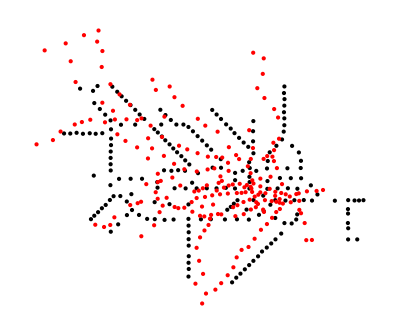

```mathematica
{undergroundMapPoints[1933]//Point,Red,globalTransformation[1933][geographicallyAccuratePoints[1933]]//Point}//Graphics
```

## Displacement Vectors

A simple way of visualizing the distortion, is simply to associate each reference point to where it would like had the map been ‘as accurate’ as the geographically accurate locations

Meaning we’ll draw displacement vectors from the transportation map stations to the respective locations following our global transformation

```mathematica
displacementVectors[year_]:=With[{tf=globalTransformation[year]},
tf[geographicallyAccuratePoints[year]]-undergroundMapPoints[year]]
```

```mathematica
displacementVectorsGraphicsPrimitive[year_]:=With[
{vecs=displacementVectors[year],controlPoints=undergroundMapPoints[year]},
Arrow/@Thread[{controlPoints,controlPoints+vecs}]]
```

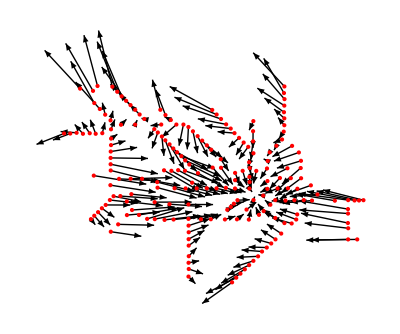

```mathematica
{Arrowheads[Medium],displacementVectorsGraphicsPrimitive[1933],Red,Point[undergroundMapPoints[1933]]}//Graphics
```

## Distortion Grids

To go further, we wish to setup a local grid and see how it transforms to accommodate the displacement vectors

We start with a regularly spaced grid spanning the geographically accurate map’s coordinate system

and distort it (rotate, scale, translate) according to the global transformation above

```mathematica
undistortedGridStraight[delta_]:=Block[{minX,maxX,minY,maxY},
{{minX,maxX},{minY,maxY}}=Thread[{1,ImageDimensions[geographicallyAccurateMap[2014]]}];

minX=Floor[minX,delta];
minY=Floor[minY,delta];
maxX=Ceiling[maxX,delta];
maxY=Ceiling[maxY,delta];

Tuples[{Range[minX,maxX,delta],Range[minY,maxY,delta]}]
]

undistortedGrid[year_,delta_:20]:=With[{tf=globalTransformation[year]},
tf[undistortedGridStraight[delta]]]
```

```mathematica
Style[Graphics[{PointSize[Small],undistortedGrid[1933,40]//Point},ImageSize->400],Antialiasing->True]//Rasterize
```

-Graphics-

A (hacky) way of joining nearest points to display a grid

```mathematica
Clear[pointsToGridsGraphicsPrimitive]
thread[first_,rest___]:=Thread[{first,{rest}}]
pointsToGridsGraphicsPrimitive[year_,delta_:20]:=pointsToGridsGraphicsPrimitive[year]=Block[{scale=Max[Most[Diagonal[globalTransformation[year][[1]]]]],nf=Nearest[undistortedGrid[year,delta]->Automatic]},
Line/@DeleteDuplicates[Join@@thread@@@(nf[#,{All,1.05 scale delta}]&/@undistortedGrid[year,delta])]]
undistortedGridGraphicsPrimitive[year_,delta_:20]:=GraphicsComplex[undistortedGrid[year,delta],pointsToGridsGraphicsPrimitive[year,delta]]
```

```mathematica
Style[Graphics[undistortedGridGraphicsPrimitive[1933,40],ImageSize->400],Antialiasing->True]//Rasterize
```

-Graphics-

We can the use a multi-quadratic interpolation to extract the local grid displacements to match the displacement vectors

[U
V]=[D | 0
0 | D]•[a
b]

where U, V are vectors of horizontal and vertical displacement vectors respectively,

the block diagonal matrix is constructed using the DistanceMatrix of the d_ii between reference points p_i and p_j

and a,b are the vectors of local transformation parameters we’re trying to fit

```mathematica
distanceMatrix[year_]:=DistanceMatrix[undergroundMapPoints[year]]
```

```mathematica
multiquadraticInterpolationFit[year_]:=Block[
{
m=ArrayFlatten[
{{distanceMatrix[year],0},{0,distanceMatrix[year]}}
],
b=Flatten[Transpose[displacementVectors[year]]]},
LinearSolve[m,b]
]
```

The distorted grid’s displacement vectors are then given by the weighted sum:

U^*= a • S
	V^*= b • S

where S_ij is the distance b/w the reference point p_i and grid point vertex s_j

```mathematica
distortedGridDisplacements[year_,delta_:20]:=Block[{horizontalFit,verticalFit,dm,l,horizontalDisplacements,verticalDisplacements},
l=Length[undergroundMapPoints[year]];
{horizontalFit,verticalFit}=Partition[multiquadraticInterpolationFit[year],l];
dm=DistanceMatrix[undistortedGrid[year,delta],undergroundMapPoints[year]];
horizontalDisplacements=dm.horizontalFit;
verticalDisplacements=dm.verticalFit;
Thread[{horizontalDisplacements,verticalDisplacements}]]
```

Putting everything together to construct our displacement grid:

```mathematica
distortedGrid[year_,delta_:20]:=undistortedGrid[year,delta]+distortedGridDisplacements[year,delta]
distortedGridGraphicsPrimitive[year_,delta_:20]:=GraphicsComplex[distortedGrid[year,delta],pointsToGridsGraphicsPrimitive[year,delta]]
```

```mathematica
Clear[visualizeDistortedGrids]
visualizeDistortedGrids[year_,delta_:20]:=visualizeDistortedGrids[year,delta]=Graphics[{
{Opacity[0.5],Thin,Gray,undistortedGridGraphicsPrimitive[year,delta]},
{Black,Thin,distortedGridGraphicsPrimitive[year,delta]},
{Blue,Arrowheads[Small],displacementVectorsGraphicsPrimitive[year]},
{Red,PointSize[Medium],Point[undergroundMapPoints[year]]}},ImageSize->600]
```

```mathematica
visualizeDistortedGrids[1948,40]//Rasterize
```

-Graphics-

And overlay the distortion grid on our transportation map

```mathematica
Clear[overlayedDistortedMap]
overlayedDistortedMap[year_,delta_:20]:=overlayedDistortedMap[year,delta]=With[{dims=distortedMap[year]//ImageDimensions},
ImageCompose[distortedMap[year],Rasterize[Graphics[{Thickness[0.00005],distortedGridGraphicsPrimitive[year,delta]},PlotRange->Thread[{1,dims}],PlotRangePadding->None,PlotRangeClipping->True,Background->None],
RasterSize->dims,ImageSize->dims,Background->None]]]
```

```mathematica
Rasterize[overlayedDistortedMap[1933,5],RasterSize->800]
```

-Graphics-

And a look at the first six London underground distorted grid maps

```mathematica
Rasterize[Multicolumn[Table[Show[overlayedDistortedMap[year,5],ImageSize->600,PlotLabel->Style[StringTemplate["London Underground Distorted Grid Map `1`"][year],24,Black]],{year,referenceYears}],2,Appearance->"Horizontal"],RasterSize->1200]
```

-Graphics-